# Neutral atoms/Rydberg qubits

## Consultants : Natalie Pearson, Tomas Kozlej, Jonathan Pritchard, Andrew

Set environment, such as threads, gpu, etc.

```mathematica
SetEnvironment["OMP_NUM_THREADS"->"8"]
SetDirectory[NotebookDirectory[]];
```

Load the QuESTLink

```mathematica
Import["/home/cica/programs/QuESTlink/Link/QuESTlink.m"];
CreateLocalQuESTEnv["quest_link_cpu"];
```

Virtual quantum devices, loaded after questlink

```mathematica
Get["../vqd.wl"]
```

Time unit : μs
Frequency unit: MHz
Length unit: μm

Accepts 2 or 3 dimensional coordinate format

```mathematica
(* 2d-array of 9 atoms*)
locs2=Association@MapThread[#->#2&,{Range[0,8],Flatten[Table[{i,j},{i,0,2},{j,0,2}],1]}];
(* 3d-array of 27 atoms *)
locs3=Association@MapThread[#->#2&,{Range[0,26],Flatten[Table[{i,j,k},{i,0,2},{j,0,2},{k,0,2}],2]}];
```

Specification of the device

```mathematica
Options[RydbergHub]={
(* The total number of physical qubits *)
qubitsNum-> 9,
(*Physical location on each qubit described with 3D-vector*)
AtomLocations->locs2,
(* It's presumed that Subscript[T, 2]^* has been echoed out to Subscript[T, 2] *)
T2->100*10^6,
(* vacuum life time, where T1=τvac/N in μs *)
VacLifeTime->100*10^6,
(* Rabi frequency MHz *)
RabiFreq->0.1,
(* Unit lattice in μm. This will be the unit of the lattice/locations given in qubitLocations *)
UnitLattice->1,
(* blockade radius in μm*)
BlockadeRadius->Sqrt@2,
(* Leakage probability in the initalisation *)
ProbLeakInit->0.01,
(* duration on the initialization *)
DurInit->5*10^5,
(* measurement induces atom loss afterward *)
FidMeas-> 0.987,
DurMeas-> 10,
(* The increasing probability of atom loss on each measurement. The value keeps increasing until being initialised *)
ProbLossMeas-> 0.05,
(* leak probability of implementing multi-qubit gates *)
ProbLeakCZ-> <|01-> 0.001,11->0.001 |>
};
```

```mathematica
PlotAtoms[RydbergHub[qubitsNum->27,AtomLocations->locs3,UnitLattice->1.5],ShowBlockade->{5,7,8},ShowLossAtoms->True]
```

-Graphics3D-

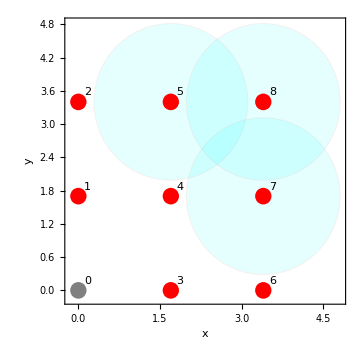

```mathematica
PlotAtoms[RydbergHub[qubitsNum->9,AtomLocations->locs2,UnitLattice->1.7],ShowBlockade->{5,7,8},ShowLossAtoms->True,ImageSize->Medium]
```